Vaje 5: 2.domača naloga

Naloga 1:

```mathematica
d=Daljica[{-1,1},{3,-1}]
```

Daljica[{-1,1},{3,-1}]

```mathematica
Dolzina[Daljica[AA_,BB_]] := Norm[BB-AA]
```

```mathematica
Dolzina[d]
```

2 √5

```mathematica
EnacbaNosilke[Daljica[AA_,BB_]] := Module[{x1, y1, x2, y2, n, k},
{x1, y1}= AA;
{x2, y2} = BB;
k= (y2-y1)/(x2-x1);
n= n/.First[Solve[y1== k*x1+n,n]];
y == k*x+n]
```

```mathematica
EnacbaNosilke[d]
```

y==1/2-x/2

```mathematica
Slika[Daljica[AA_,BB_]] := Line [{AA, BB}]
```

```mathematica
Slika[d]
```

Line[{{-1,1},{3,-1}}]

```mathematica
Narisi[d_] := Graphics[Slika[d]]
```

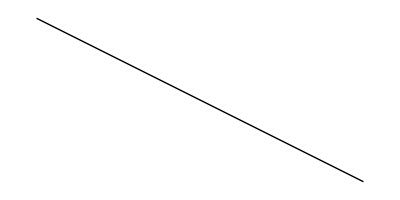

```mathematica
Narisi[d]
```

Naloga 2:

```mathematica
dd=Daljica[{-4,5},{55,-32}]
```

Daljica[{-4,5},{55,-32}]

```mathematica
Presek[Daljica[AA_,BB_],Daljica[CC_,DD_]] := Module[{a, b},
a = EnacbaNosilke[d];
b = EnacbaNosilke[dd];
rešitev= Solve[a&&b, {x, y}]]
```

```mathematica
Presek[d,dd]
```

{{x→47/3,y→-22/3}}

Naloga 3:

```mathematica
ClearAll[Slika]
```

```mathematica
m1=Mnogokotnik[{0,0},{1,1},{0,3},{-1,2}]
```

Mnogokotnik[{0,0},{1,1},{0,3},{-1,2}]

```mathematica
Slika[Mnogokotnik[t__]]:=Line[{{0,0},{1,1},{0,3},{-1,2},First[m1]}]
```

```mathematica
Slika[m1]
```

Line[{{0,0},{1,1},{0,3},{-1,2},{0,0}}]

```mathematica
Narisi[m1_] := Graphics[Slika[m1]]
```

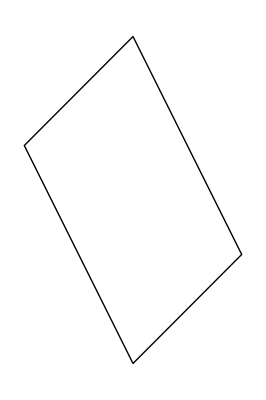

```mathematica
Narisi[m1]
```

```mathematica
PravilniNKotnik[n_,r_]:= Graphics[{Line[Table[{r* Cos[(2Pi * i)/n],r*Sin[(2 Pi *i)/n]},{i,0,n}]]}]
```

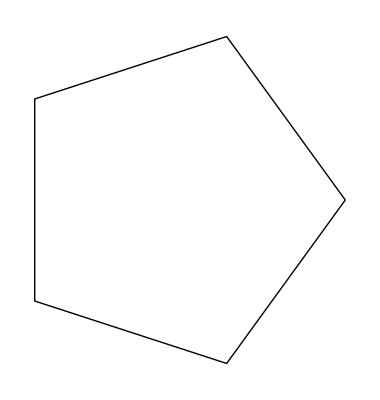

```mathematica
PravilniNKotnik[5,2]
```

```mathematica
PravilniNKotnik[n_,r_,phi_] := Graphics[{Line[Table[{r*Cos[(2Pi*i+phi)/n ],r*Sin[(2Pi*i+phi)/n]},{i,0,n}]],Point[{0,0}]}]
Manipulate[PravilniNKotnik[5,2,phi],{phi,1.57,33}]
```

Naloga 4:

Naloga 5:

```mathematica
VsiPari[f_,sez1_,sez2_]:=Flatten[Outer[f,sez1,sez2],1]
VsiPari[f,{1,2,3},{a,b}]
```

{f[1,a],f[1,b],f[2,a],f[2,b],f[3,a],f[3,b]}

```mathematica
siPari[f_,sez1_,sez2_]:=Flatten[Outer[f,sez1,sez2],1]
VsiPari[{1,2,3},{2,8,6},{4,5}]
```

{{1,2,3}[2,4],{1,2,3}[2,5],{1,2,3}[8,4],{1,2,3}[8,5],{1,2,3}[6,4],{1,2,3}[6,5]}

```mathematica
z = List[{1,2,3},{2,8,6},{4,5}]
```

{{1,2,3},{2,8,6},{4,5}}

```mathematica
P3 =Flatten[z]
```

{1,2,3,2,8,6,4,5}

```mathematica
P4= Outer[f,z,z]
```

{{{{f[1,1],f[1,2],f[1,3]},{f[1,2],f[1,8],f[1,6]},{f[1,4],f[1,5]}},{{f[2,1],f[2,2],f[2,3]},{f[2,2],f[2,8],f[2,6]},{f[2,4],f[2,5]}},{{f[3,1],f[3,2],f[3,3]},{f[3,2],f[3,8],f[3,6]},{f[3,4],f[3,5]}}},{{{f[2,1],f[2,2],f[2,3]},{f[2,2],f[2,8],f[2,6]},{f[2,4],f[2,5]}},{{f[8,1],f[8,2],f[8,3]},{f[8,2],f[8,8],f[8,6]},{f[8,4],f[8,5]}},{{f[6,1],f[6,2],f[6,3]},{f[6,2],f[6,8],f[6,6]},{f[6,4],f[6,5]}}},{{{f[4,1],f[4,2],f[4,3]},{f[4,2],f[4,8],f[4,6]},{f[4,4],f[4,5]}},{{f[5,1],f[5,2],f[5,3]},{f[5,2],f[5,8],f[5,6]},{f[5,4],f[5,5]}}}}

```mathematica
m2 =RegularPolygon[1,4]
```

RegularPolygon[1,4]

```mathematica
Presek[m1_Mnogokotnik,m2_Mnogokotnik] :=
```

Naloga 6: